```mathematica
chancep[p_,x_] = ((p+1)/(2p))^Log[p,(x+1)]
```

2^(-Log[1+x]/Log[p]) ((1+p)/p)^(Log[1+x]/Log[p])

```mathematica
FindGeneratingFunction[Table[FullSimplify[Assuming[Element[p, Integers],Sum[chancep[p,i],{i,1,n}]]],{n,0,10}],x]
```

$Aborted

```mathematica
Good3 [d_] := Table[FromDigits [n,3], {n,Select[IntegerString[Range[d-1], 3],Not[ StringMatchQ[# , "*2*"]]&]}]
```

```mathematica
Good3[200]
```

{1,3,4,9,10,12,13,27,28,30,31,36,37,39,40,81,82,84,85,90,91,93,94,108,109,111,112,117,118,120,121}

```mathematica
Count3[x_] := Length[Good3[x]]
```

```mathematica
First[Flatten[StringPosition["345","5",1]]
```

{3,3}

```mathematica
PGood[p,n]:=Block [ {result}, result={};Do[If[IntegerDigits[i,p] < (p+1)/2, result = Append[result,i]], {i,0,10}]]
```

```mathematica
PGood[3,10]
```

PGood[3,10]

```mathematica
result={};Do[If[IntegerDigits[i,3] < 2, result = Append[result,i]], {i,0,10}]
```

```mathematica
FindGeneratingFunction[{0,1,3,4,9,10},x,FunctionSpace->"RationalFunction"]
```

```mathematica
FindGeneratingFunction[{0,1,3,4,9,10},x,FunctionSpace->All]
```

```mathematica
Count3[9]
```

4

```mathematica
Count3[9]
```

Count3[9]

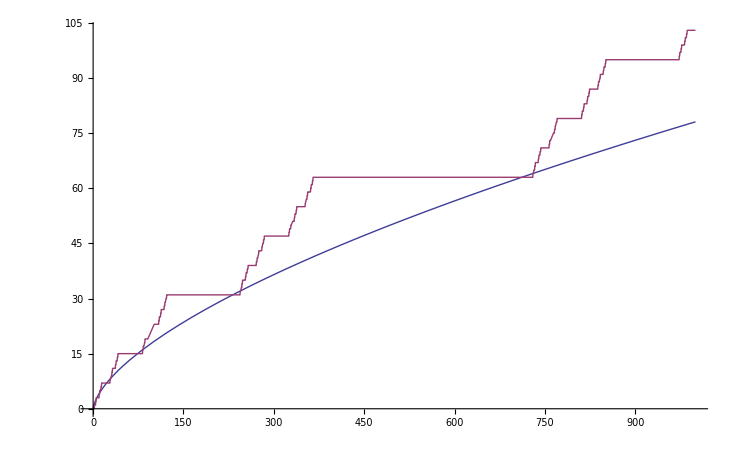

```mathematica
Plot[{x * chancep[3,x], Count3[x]}, {x,0,1000}]
```

```mathematica
Table[Prime[t],{t,120,140}]
```

{659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809}

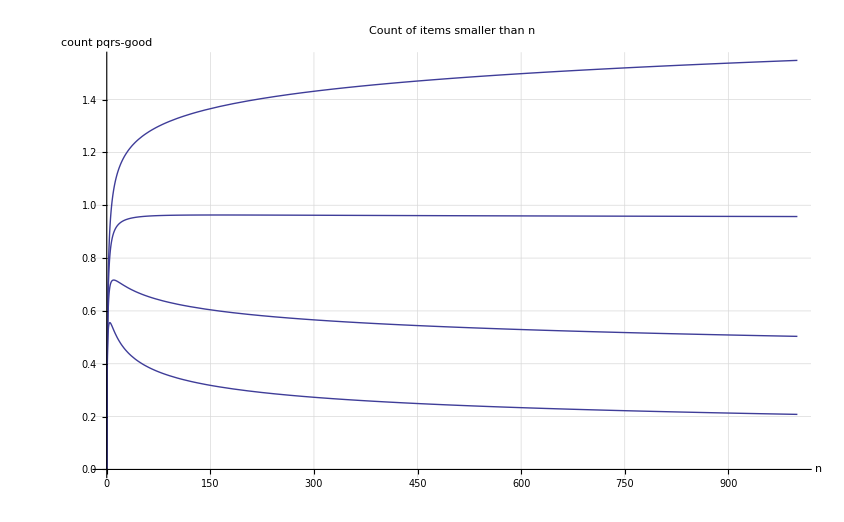

```mathematica
Show[
Table[
Plot[chancep[Prime[n],x]chancep[Prime[n+1],x]chancep[Prime[n+2],x] chancep[Prime[n+3],x]  x, {x,0,1000},  PlotLabel->"Count of items smaller than n",AxesLabel->{"n","count pqrs-good"},LabelStyle->{FontFamily->"Calibri", 
FontSize->Larger},
GridLines->Automatic, 
PlotRange->{All,All}
],
{n,2,5}]
]
```

```mathematica
Table[FullSimplify[chancep[Prime[n],x]chancep[Prime[n+1],x]chancep[Prime[n+2],x] chancep[Prime[n+3],x]  x],
{n,2,10}]
```

{x (1+x)^(-4+Log[4]/Log[7]+Log[2] (1/Log[3]+1/Log[11])+(Log[3] Log[55])/(Log[5] Log[11])),x (1+x)^(-4+Log[3]/Log[5]+Log[4]/Log[7]+Log[6]/Log[11]+Log[7]/Log[13]),x (1+x)^(-4+Log[4]/Log[7]+Log[6]/Log[11]+Log[7]/Log[13]+Log[9]/Log[17]),x (1+x)^(-4+Log[7]/Log[13]+((Log[5] Log[11]+Log[2] Log[209])/Log[19]+(Log[3] Log[2057])/Log[17])/Log[11]),x (1+x)^(-4+Log[7]/Log[13]+((Log[5] Log[23]+Log[2] Log[8303])/Log[19]+(Log[3] Log[8993])/Log[17])/Log[23]),x (1+x)^(-4+Log[9]/Log[17]+(Log[5] Log[23] Log[551]+Log[3] Log[19] Log[667]+Log[2] Log[29] Log[8303])/(Log[19] Log[23] Log[29])),x (1+x)^(-4+Log[4]/Log[23]+Log[16]/Log[31]+((Log[2] Log[29]+Log[5] Log[551])/Log[19]+(Log[3] Log[667])/Log[23])/Log[29]),x (1+x)^(-4+Log[19]/Log[37]+((Log[5] Log[23]+Log[3] Log[667])/Log[29]+(Log[4] Log[16399])/Log[31])/Log[23]),x (1+x)^(-4+Log[15]/Log[29]+Log[16]/Log[31]+Log[19]/Log[37]+Log[21]/Log[41])}

```mathematica
Table[FullSimplify[D [chancep[Prime[n],x]chancep[Prime[n+1],x]chancep[Prime[n+2],x] chancep[Prime[n+3],x]  x, x]],
{n,2,10}]
```

{1/(Log[3] Log[5] Log[7] Log[11])(1+x)^(-5+Log[4]/Log[7]+(Log[2] Log[33])/(Log[3] Log[11])+(Log[3] Log[55])/(Log[5] Log[11])) (Log[7] (Log[3] Log[5] Log[11]+x Log[2] Log[5] Log[33]+x Log[3]^2 Log[55])-x Log[3] Log[5] Log[11] Log[343/4]),1/(Log[5] Log[7] Log[11] Log[13])(1+x)^(-5+Log[3]/Log[5]+Log[4]/Log[7]+Log[6]/Log[11]+Log[7]/Log[13]) (Log[11] (x Log[5] Log[7]^2+(x Log[4] Log[5]+(x Log[3]+Log[5]) Log[7]) Log[13])-x Log[5] Log[7] Log[13] Log[1331/6]),1/(Log[7] Log[11] Log[13] Log[17])(1+x)^(-5+Log[4]/Log[7]+Log[6]/Log[11]+Log[7]/Log[13]+Log[9]/Log[17]) (Log[11] (x Log[7] Log[9] Log[13]+(x Log[7]^2+(x Log[4]+Log[7]) Log[13]) Log[17])-x Log[7] Log[13] Log[17] Log[1331/6]),1/(Log[11] Log[13] Log[17] Log[19])(1+x)^(-5+Log[6]/Log[11]+Log[7]/Log[13]+Log[9]/Log[17]+Log[10]/Log[19]) (Log[17] (Log[13] (Log[11] (x Log[5]+Log[19])+x Log[2] Log[209])-x Log[11] Log[19] Log[2197/7])+x Log[3] Log[13] Log[19] Log[2057]),1/(Log[13] Log[17] Log[19] Log[23])(1+x)^(-5+Log[7]/Log[13]+((Log[5] Log[23]+Log[2] Log[8303])/Log[19]+(Log[3] Log[8993])/Log[17])/Log[23]) (Log[13] (x Log[12] Log[17] Log[19]+(x Log[10] Log[17]+(x Log[9]+Log[17]) Log[19]) Log[23])-x Log[17] Log[19] Log[23] Log[2197/7]),1/(Log[17] Log[19] Log[23] Log[29])(1+x)^(-5+Log[9]/Log[17]+(Log[5] Log[23] Log[551]+Log[3] Log[19] Log[667]+Log[2] Log[29] Log[8303])/(Log[19] Log[23] Log[29])) (Log[17] Log[19] Log[23] Log[29]+x (Log[4] Log[17] Log[19] Log[29]+Log[9] Log[19] Log[23] Log[29]+Log[17] (Log[3] Log[19] Log[667]+Log[23] (Log[5] Log[551]-Log[29] Log[6859/2])))),1/(Log[19] Log[23] Log[29] Log[31])(1+x)^(-5+Log[4]/Log[23]+Log[16]/Log[31]+((Log[2] Log[29]+Log[5] Log[551])/Log[19]+(Log[3] Log[667])/Log[23])/Log[29]) (Log[19] Log[23] Log[29] Log[31]+x (Log[16] Log[19] Log[23] Log[29]+Log[31] (Log[5] Log[23] Log[551]+Log[19] (Log[4] Log[29]+Log[3] Log[667])-Log[23] Log[29] Log[6859/2]))),1/(Log[23] Log[29] Log[31] Log[37])(1+x)^(-5+Log[19]/Log[37]+((Log[5] Log[23]+Log[3] Log[667])/Log[29]+(Log[4] Log[16399])/Log[31])/Log[23]) (Log[23] Log[29] Log[31] Log[37]+x (Log[19] Log[23] Log[29] Log[31]+Log[37] (Log[16] Log[23] Log[29]+Log[31] (Log[23] (Log[5]-3 Log[29])+Log[4] Log[29]+Log[3] Log[667])))),1/(Log[29] Log[31] Log[37] Log[41])(1+x)^(-5+Log[15]/Log[29]+Log[16]/Log[31]+Log[19]/Log[37]+Log[21]/Log[41]) (Log[29] Log[31] Log[37] Log[41]+x (Log[7] Log[29] Log[31] Log[37]+(Log[19] Log[29] Log[31]+(Log[29] (Log[16]-3 Log[31])+Log[5] Log[31]) Log[37]) Log[41]+Log[3] Log[31] Log[37] Log[1189]))}

```mathematica
FullSimplify[-(2^(Log[1+x]/Log[3]+(2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(1-Log[1+x]/Log[3]+Log[1+x]/Log[5]+Log[1+x]/Log[11]) x)/(1+x)^4+(2^(Log[1+x]/Log[3]+(2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(-Log[1+x]/Log[3]+Log[1+x]/Log[5]+Log[1+x]/Log[11]))/(1+x)^3+(2^(Log[1+x]/Log[3]+(2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(-Log[1+x]/Log[3]+Log[1+x]/Log[5]+Log[1+x]/Log[11]) x Log[3] (-1/((1+x) Log[3])+1/((1+x) Log[5])+1/((1+x) Log[11])))/(1+x)^3+(2^(Log[1+x]/Log[3]+(2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(-Log[1+x]/Log[3]+Log[1+x]/Log[5]+Log[1+x]/Log[11]) x Log[2] (1/((1+x) Log[3])+2/((1+x) Log[7])+1/((1+x) Log[11])))/(1+x)^3]
```

1/(Log[3] Log[5] Log[7] Log[11])(1+x)^(-5+Log[4]/Log[7]+(Log[2] Log[33])/(Log[3] Log[11])+(Log[3] Log[55])/(Log[5] Log[11])) (Log[7] (Log[3] Log[5] Log[11]+x Log[2] Log[5] Log[33]+x Log[3]^2 Log[55])-x Log[3] Log[5] Log[11] Log[343/4])

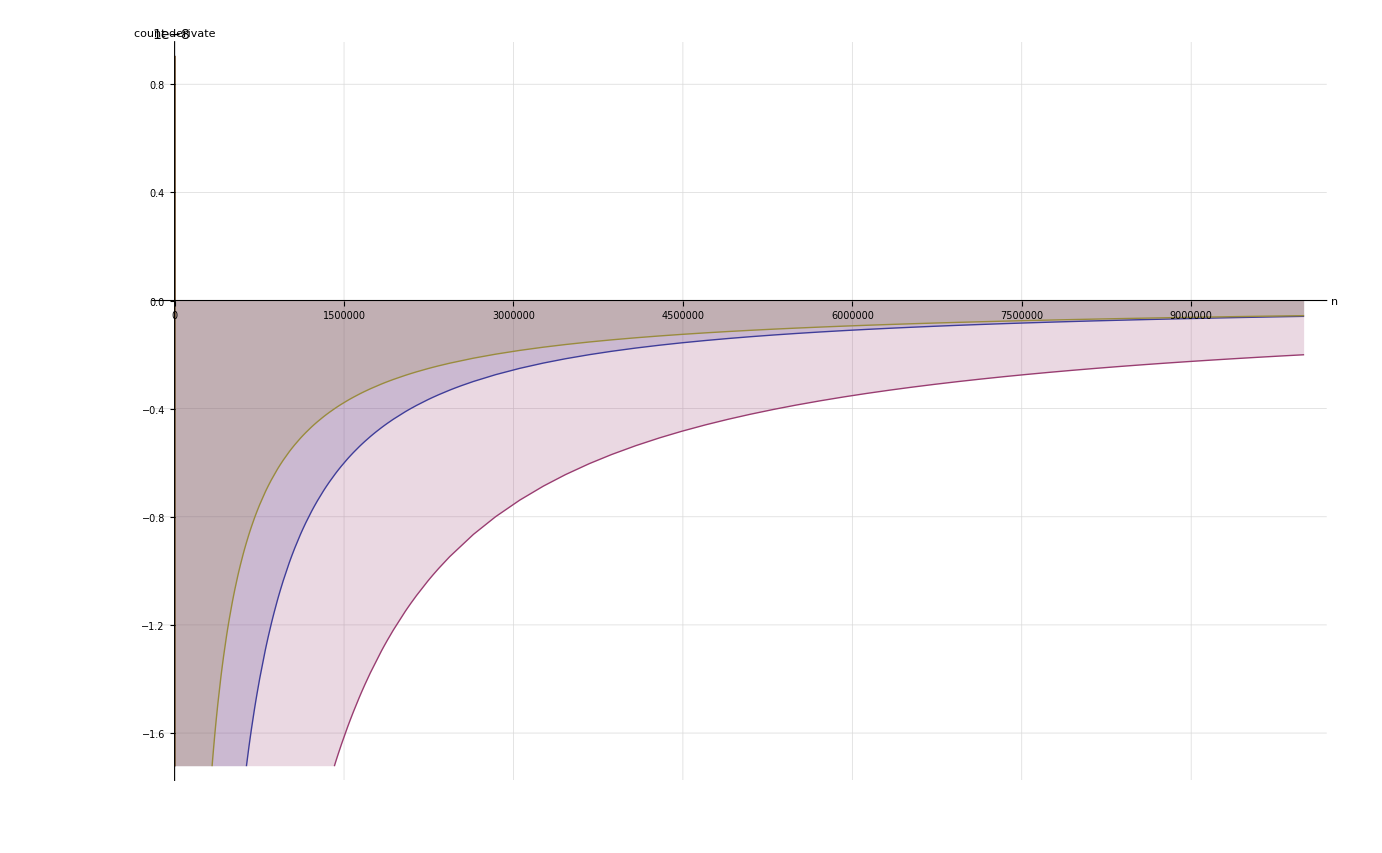

```mathematica
Show[
Plot[{-(2^(Log[1+x]/Log[3]+(2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(1-Log[1+x]/Log[3]+Log[1+x]/Log[5]+Log[1+x]/Log[11]) x)/(1+x)^4+(2^(Log[1+x]/Log[3]+(2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(-Log[1+x]/Log[3]+Log[1+x]/Log[5]+Log[1+x]/Log[11]))/(1+x)^3+(2^(Log[1+x]/Log[3]+(2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(-Log[1+x]/Log[3]+Log[1+x]/Log[5]+Log[1+x]/Log[11]) x Log[3] (-1/((1+x) Log[3])+1/((1+x) Log[5])+1/((1+x) Log[11])))/(1+x)^3+(2^(Log[1+x]/Log[3]+(2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(-Log[1+x]/Log[3]+Log[1+x]/Log[5]+Log[1+x]/Log[11]) x Log[2] (1/((1+x) Log[3])+2/((1+x) Log[7])+1/((1+x) Log[11])))/(1+x)^3,-(2^(2+(2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(Log[1+x]/Log[5]+Log[1+x]/Log[11]) ⅇ^((Log[7] Log[1+x])/Log[13]) x)/(1+x)^5+(2^((2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(Log[1+x]/Log[5]+Log[1+x]/Log[11]) ⅇ^((Log[7] Log[1+x])/Log[13]))/(1+x)^4+(2^((2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(Log[1+x]/Log[5]+Log[1+x]/Log[11]) ⅇ^((Log[7] Log[1+x])/Log[13]) x Log[3] (1/((1+x) Log[5])+1/((1+x) Log[11])))/(1+x)^4+(2^((2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(Log[1+x]/Log[5]+Log[1+x]/Log[11]) ⅇ^((Log[7] Log[1+x])/Log[13]) x Log[2] (2/((1+x) Log[7])+1/((1+x) Log[11])))/(1+x)^4+(2^((2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(Log[1+x]/Log[5]+Log[1+x]/Log[11]) ⅇ^((Log[7] Log[1+x])/Log[13]) x Log[7])/((1+x)^5 Log[13]),-(2^(2+(2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(Log[1+x]/Log[11]+(2 Log[1+x])/Log[17]) ⅇ^((Log[7] Log[1+x])/Log[13]) x)/(1+x)^5+(2^((2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(Log[1+x]/Log[11]+(2 Log[1+x])/Log[17]) ⅇ^((Log[7] Log[1+x])/Log[13]))/(1+x)^4+(2^((2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(Log[1+x]/Log[11]+(2 Log[1+x])/Log[17]) ⅇ^((Log[7] Log[1+x])/Log[13]) x Log[2] (2/((1+x) Log[7])+1/((1+x) Log[11])))/(1+x)^4+(2^((2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(Log[1+x]/Log[11]+(2 Log[1+x])/Log[17]) ⅇ^((Log[7] Log[1+x])/Log[13]) x Log[7])/((1+x)^5 Log[13])+(2^((2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(Log[1+x]/Log[11]+(2 Log[1+x])/Log[17]) ⅇ^((Log[7] Log[1+x])/Log[13]) x Log[3] (1/((1+x) Log[11])+2/((1+x) Log[17])))/(1+x)^4(*,-(2^(2+Log[1+x]/Log[11]+Log[1+x]/Log[19]) 3^(Log[1+x]/Log[11]+(2 Log[1+x])/Log[17]) 5^(Log[1+x]/Log[19]) 7^(Log[1+x]/Log[13]) x)/(1+x)^5+(2^(Log[1+x]/Log[11]+Log[1+x]/Log[19]) 3^(Log[1+x]/Log[11]+(2 Log[1+x])/Log[17]) 5^(Log[1+x]/Log[19]) 7^(Log[1+x]/Log[13]))/(1+x)^4+(2^(Log[1+x]/Log[11]+Log[1+x]/Log[19]) 3^(Log[1+x]/Log[11]+(2 Log[1+x])/Log[17]) 5^(Log[1+x]/Log[19]) 7^(Log[1+x]/Log[13]) x Log[7])/((1+x)^5 Log[13])+(2^(Log[1+x]/Log[11]+Log[1+x]/Log[19]) 3^(Log[1+x]/Log[11]+(2 Log[1+x])/Log[17]) 5^(Log[1+x]/Log[19]) 7^(Log[1+x]/Log[13]) x Log[3] (1/((1+x) Log[11])+2/((1+x) Log[17])))/(1+x)^4+(2^(Log[1+x]/Log[11]+Log[1+x]/Log[19]) 3^(Log[1+x]/Log[11]+(2 Log[1+x])/Log[17]) 5^(Log[1+x]/Log[19]) 7^(Log[1+x]/Log[13]) x Log[2] (1/((1+x) Log[11])+1/((1+x) Log[19])))/(1+x)^4+(2^(Log[1+x]/Log[11]+Log[1+x]/Log[19]) 3^(Log[1+x]/Log[11]+(2 Log[1+x])/Log[17]) 5^(Log[1+x]/Log[19]) 7^(Log[1+x]/Log[13]) x Log[5])/((1+x)^5 Log[19]),-(2^(2+Log[1+x]/Log[19]+(2 Log[1+x])/Log[23]) 3^((2 Log[1+x])/Log[17]+Log[1+x]/Log[23]) 5^(Log[1+x]/Log[19]) 7^(Log[1+x]/Log[13]) x)/(1+x)^5+(2^(Log[1+x]/Log[19]+(2 Log[1+x])/Log[23]) 3^((2 Log[1+x])/Log[17]+Log[1+x]/Log[23]) 5^(Log[1+x]/Log[19]) 7^(Log[1+x]/Log[13]))/(1+x)^4+(2^(Log[1+x]/Log[19]+(2 Log[1+x])/Log[23]) 3^((2 Log[1+x])/Log[17]+Log[1+x]/Log[23]) 5^(Log[1+x]/Log[19]) 7^(Log[1+x]/Log[13]) x Log[7])/((1+x)^5 Log[13])+(2^(Log[1+x]/Log[19]+(2 Log[1+x])/Log[23]) 3^((2 Log[1+x])/Log[17]+Log[1+x]/Log[23]) 5^(Log[1+x]/Log[19]) 7^(Log[1+x]/Log[13]) x Log[5])/((1+x)^5 Log[19])+(2^(Log[1+x]/Log[19]+(2 Log[1+x])/Log[23]) 3^((2 Log[1+x])/Log[17]+Log[1+x]/Log[23]) 5^(Log[1+x]/Log[19]) 7^(Log[1+x]/Log[13]) x Log[3] (2/((1+x) Log[17])+1/((1+x) Log[23])))/(1+x)^4+(2^(Log[1+x]/Log[19]+(2 Log[1+x])/Log[23]) 3^((2 Log[1+x])/Log[17]+Log[1+x]/Log[23]) 5^(Log[1+x]/Log[19]) 7^(Log[1+x]/Log[13]) x Log[2] (1/((1+x) Log[19])+2/((1+x) Log[23])))/(1+x)^4,-(2^(2+Log[1+x]/Log[19]+(2 Log[1+x])/Log[23]) 3^((2 Log[1+x])/Log[17]+Log[1+x]/Log[23]+Log[1+x]/Log[29]) 5^(Log[1+x]/Log[19]+Log[1+x]/Log[29]) x)/(1+x)^5+(2^(Log[1+x]/Log[19]+(2 Log[1+x])/Log[23]) 3^((2 Log[1+x])/Log[17]+Log[1+x]/Log[23]+Log[1+x]/Log[29]) 5^(Log[1+x]/Log[19]+Log[1+x]/Log[29]))/(1+x)^4+(2^(Log[1+x]/Log[19]+(2 Log[1+x])/Log[23]) 3^((2 Log[1+x])/Log[17]+Log[1+x]/Log[23]+Log[1+x]/Log[29]) 5^(Log[1+x]/Log[19]+Log[1+x]/Log[29]) x Log[2] (1/((1+x) Log[19])+2/((1+x) Log[23])))/(1+x)^4+(2^(Log[1+x]/Log[19]+(2 Log[1+x])/Log[23]) 3^((2 Log[1+x])/Log[17]+Log[1+x]/Log[23]+Log[1+x]/Log[29]) 5^(Log[1+x]/Log[19]+Log[1+x]/Log[29]) x Log[5] (1/((1+x) Log[19])+1/((1+x) Log[29])))/(1+x)^4+(2^(Log[1+x]/Log[19]+(2 Log[1+x])/Log[23]) 3^((2 Log[1+x])/Log[17]+Log[1+x]/Log[23]+Log[1+x]/Log[29]) 5^(Log[1+x]/Log[19]+Log[1+x]/Log[29]) x Log[3] (2/((1+x) Log[17])+1/((1+x) Log[23])+1/((1+x) Log[29])))/(1+x)^4,-(2^(2+Log[1+x]/Log[19]+(2 Log[1+x])/Log[23]+(4 Log[1+x])/Log[31]) 3^(Log[1+x]/Log[23]+Log[1+x]/Log[29]) 5^(Log[1+x]/Log[19]+Log[1+x]/Log[29]) x)/(1+x)^5+(2^(Log[1+x]/Log[19]+(2 Log[1+x])/Log[23]+(4 Log[1+x])/Log[31]) 3^(Log[1+x]/Log[23]+Log[1+x]/Log[29]) 5^(Log[1+x]/Log[19]+Log[1+x]/Log[29]))/(1+x)^4+(2^(Log[1+x]/Log[19]+(2 Log[1+x])/Log[23]+(4 Log[1+x])/Log[31]) 3^(Log[1+x]/Log[23]+Log[1+x]/Log[29]) 5^(Log[1+x]/Log[19]+Log[1+x]/Log[29]) x Log[5] (1/((1+x) Log[19])+1/((1+x) Log[29])))/(1+x)^4+(2^(Log[1+x]/Log[19]+(2 Log[1+x])/Log[23]+(4 Log[1+x])/Log[31]) 3^(Log[1+x]/Log[23]+Log[1+x]/Log[29]) 5^(Log[1+x]/Log[19]+Log[1+x]/Log[29]) x Log[3] (1/((1+x) Log[23])+1/((1+x) Log[29])))/(1+x)^4+(2^(Log[1+x]/Log[19]+(2 Log[1+x])/Log[23]+(4 Log[1+x])/Log[31]) 3^(Log[1+x]/Log[23]+Log[1+x]/Log[29]) 5^(Log[1+x]/Log[19]+Log[1+x]/Log[29]) x Log[2] (1/((1+x) Log[19])+2/((1+x) Log[23])+4/((1+x) Log[31])))/(1+x)^4,-(3^(Log[1+x]/Log[23]+Log[1+x]/Log[29]) 4^(1+Log[1+x]/Log[23]+(2 Log[1+x])/Log[31]) 5^(Log[1+x]/Log[29]) 19^(Log[1+x]/Log[37]) x)/(1+x)^5+(3^(Log[1+x]/Log[23]+Log[1+x]/Log[29]) 4^(Log[1+x]/Log[23]+(2 Log[1+x])/Log[31]) 5^(Log[1+x]/Log[29]) 19^(Log[1+x]/Log[37]))/(1+x)^4+(3^(Log[1+x]/Log[23]+Log[1+x]/Log[29]) 4^(Log[1+x]/Log[23]+(2 Log[1+x])/Log[31]) 5^(Log[1+x]/Log[29]) 19^(Log[1+x]/Log[37]) x Log[3] (1/((1+x) Log[23])+1/((1+x) Log[29])))/(1+x)^4+(3^(Log[1+x]/Log[23]+Log[1+x]/Log[29]) 4^(Log[1+x]/Log[23]+(2 Log[1+x])/Log[31]) 5^(Log[1+x]/Log[29]) 19^(Log[1+x]/Log[37]) x Log[5])/((1+x)^5 Log[29])+(3^(Log[1+x]/Log[23]+Log[1+x]/Log[29]) 4^(Log[1+x]/Log[23]+(2 Log[1+x])/Log[31]) 5^(Log[1+x]/Log[29]) 19^(Log[1+x]/Log[37]) x Log[4] (1/((1+x) Log[23])+2/((1+x) Log[31])))/(1+x)^4+(3^(Log[1+x]/Log[23]+Log[1+x]/Log[29]) 4^(Log[1+x]/Log[23]+(2 Log[1+x])/Log[31]) 5^(Log[1+x]/Log[29]) 19^(Log[1+x]/Log[37]) x Log[19])/((1+x)^5 Log[37]),-(3^(Log[1+x]/Log[29]+Log[1+x]/Log[41]) 4^(1+(2 Log[1+x])/Log[31]) 5^(Log[1+x]/Log[29]) 7^(Log[1+x]/Log[41]) 19^(Log[1+x]/Log[37]) x)/(1+x)^5+(3^(Log[1+x]/Log[29]+Log[1+x]/Log[41]) 5^(Log[1+x]/Log[29]) 7^(Log[1+x]/Log[41]) 16^(Log[1+x]/Log[31]) 19^(Log[1+x]/Log[37]))/(1+x)^4+(3^(Log[1+x]/Log[29]+Log[1+x]/Log[41]) 5^(Log[1+x]/Log[29]) 7^(Log[1+x]/Log[41]) 16^(Log[1+x]/Log[31]) 19^(Log[1+x]/Log[37]) x Log[5])/((1+x)^5 Log[29])+(3^(Log[1+x]/Log[29]+Log[1+x]/Log[41]) 5^(Log[1+x]/Log[29]) 7^(Log[1+x]/Log[41]) 16^(Log[1+x]/Log[31]) 19^(Log[1+x]/Log[37]) x Log[16])/((1+x)^5 Log[31])+(3^(Log[1+x]/Log[29]+Log[1+x]/Log[41]) 5^(Log[1+x]/Log[29]) 7^(Log[1+x]/Log[41]) 16^(Log[1+x]/Log[31]) 19^(Log[1+x]/Log[37]) x Log[19])/((1+x)^5 Log[37])+(3^(Log[1+x]/Log[29]+Log[1+x]/Log[41]) 5^(Log[1+x]/Log[29]) 7^(Log[1+x]/Log[41]) 16^(Log[1+x]/Log[31]) 19^(Log[1+x]/Log[37]) x Log[3] (1/((1+x) Log[29])+1/((1+x) Log[41])))/(1+x)^4+(3^(Log[1+x]/Log[29]+Log[1+x]/Log[41]) 5^(Log[1+x]/Log[29]) 7^(Log[1+x]/Log[41]) 16^(Log[1+x]/Log[31]) 19^(Log[1+x]/Log[37]) x Log[7])/((1+x)^5 Log[41])*)}, {x,0,10000000},  AxesLabel->{"n","count derivate"},LabelStyle->{FontFamily->"Calibri", FontSize->Larger},GridLines->Automatic, Filling->Axis]
]
```

```mathematica
Limit[-(2^(Log[1+x]/Log[3]+(2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(1-Log[1+x]/Log[3]+Log[1+x]/Log[5]+Log[1+x]/Log[11]) x)/(1+x)^4+(2^(Log[1+x]/Log[3]+(2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(-Log[1+x]/Log[3]+Log[1+x]/Log[5]+Log[1+x]/Log[11]))/(1+x)^3+(2^(Log[1+x]/Log[3]+(2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(-Log[1+x]/Log[3]+Log[1+x]/Log[5]+Log[1+x]/Log[11]) x Log[3] (-1/((1+x) Log[3])+1/((1+x) Log[5])+1/((1+x) Log[11])))/(1+x)^3+(2^(Log[1+x]/Log[3]+(2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(-Log[1+x]/Log[3]+Log[1+x]/Log[5]+Log[1+x]/Log[11]) x Log[2] (1/((1+x) Log[3])+2/((1+x) Log[7])+1/((1+x) Log[11])))/(1+x)^3, x-> 3160 ]
```

```mathematica
N[(2^((1/Log[11]+Log[63]/(Log[3] Log[7])) Log[3161]) 3^((Log[55] Log[3161])/(Log[5] Log[11])) (Log[3] Log[7] (-9479 Log[5] Log[11]+3160 Log[3] Log[55])+3160 Log[2] Log[5] (Log[3] Log[7]+Log[11] Log[63])))/(315589451939231801 Log[3] Log[5] Log[7] Log[11])]
```

-0.0000115152

```mathematica
Limit[-(2^(2+(2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(Log[1+x]/Log[11]+(2 Log[1+x])/Log[17]) ⅇ^((Log[7] Log[1+x])/Log[13]) x)/(1+x)^5+(2^((2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(Log[1+x]/Log[11]+(2 Log[1+x])/Log[17]) ⅇ^((Log[7] Log[1+x])/Log[13]))/(1+x)^4+(2^((2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(Log[1+x]/Log[11]+(2 Log[1+x])/Log[17]) ⅇ^((Log[7] Log[1+x])/Log[13]) x Log[2] (2/((1+x) Log[7])+1/((1+x) Log[11])))/(1+x)^4+(2^((2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(Log[1+x]/Log[11]+(2 Log[1+x])/Log[17]) ⅇ^((Log[7] Log[1+x])/Log[13]) x Log[7])/((1+x)^5 Log[13])+(2^((2 Log[1+x])/Log[7]+Log[1+x]/Log[11]) 3^(Log[1+x]/Log[11]+(2 Log[1+x])/Log[17]) ⅇ^((Log[7] Log[1+x])/Log[13]) x Log[3] (1/((1+x) Log[11])+2/((1+x) Log[17])))/(1+x)^4, x-> ∞ ]
```

```mathematica
Limit[1/(Log[29] Log[31] Log[37] Log[41])(1+x)^(-5+Log[15]/Log[29]+Log[16]/Log[31]+Log[19]/Log[37]+Log[21]/Log[41]) (Log[29] Log[31] Log[37] Log[41]+x (Log[7] Log[29] Log[31] Log[37]+(Log[19] Log[29] Log[31]+(Log[29] (Log[16]-3 Log[31])+Log[5] Log[31]) Log[37]) Log[41]+Log[3] Log[31] Log[37] Log[1189])),  x-> ∞ ]
```

0

```mathematica
chancep[3,9]
```

8/27

```mathematica
chancep(p_,x_)=((p+1)/(2 p))^(Subscript[log, p](x+1))
```

```mathematica
Show[
ListPlot[Table[{x,chancep[Prime[p],x]}, {p,2,3,1}, {x,1,100}], Joined->True]
]
```

Table::itform: Argument PlotStyle → {{1, Red}, {2, Blue}} at position 4 does not have the correct form for an iterator.

ListPlot::lpn: Table[{x, chancep[Prime[p], x]}, {p, 2, 3, 1}, {x, 1, 100}, PlotStyle → {{1, Red}, {2, Blue}}] is not a list of numbers or pairs of numbers.

Show::gtype: ListPlot is not a type of graphics.

Show[ListPlot[Table[{x,chancep[Prime[p],x]},{p,2,3,1},{x,1,100},PlotStyle→{{1,Red},{2,Blue}}],Joined→True]]

```mathematica
Show[
Table[
ListPlot[Table[{x,chancep[Prime[p],x]}, {x,1,100}], Joined->True],
 {p,3,10,1}
]
]
```

```mathematica
Show[
ListLogLogPlot[Table[{x,chancep[Prime[2],x] chancep[Prime[3],x] chancep[Prime[4],x] chancep[Prime[5],x]}, {x,1,1000000}], Joined->True]
,
ListLogLogPlot[Table[{x,chancep[Prime[2],x] chancep[Prime[3],x] chancep[Prime[4],x] }, {x,1,1000000}], Joined->True]
]
```

```mathematica
FullSimplify[chancep[3,8]]
```

4/9

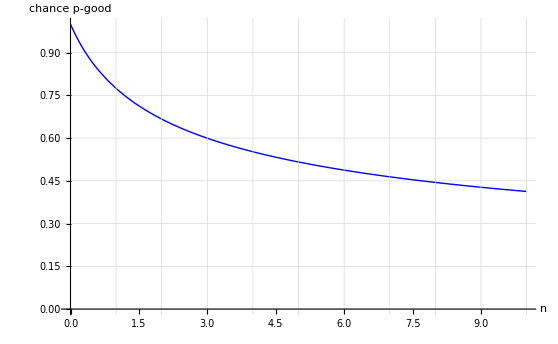

```mathematica
Plot[{chancep[3,x] }, {x,0,10},PlotStyle->{Red,Blue},  AxesLabel->{"n","chance p-good"},LabelStyle->{FontFamily->"Calibri", FontSize->Larger},GridLines->{Range[25],Automatic}, PlotRange->{Automatic, {0,1}}]
```

```mathematica
IntegerDigits[Range[0,10],3]
```

{{0},{1},{2},{1,0},{1,1},{1,2},{2,0},{2,1},{2,2},{1,0,0},{1,0,1}}

```mathematica
Subscript[log, 3](n)
```

(log(n))/(log(3))

```mathematica
(2/3)^(Subscript[log, 3](n))
```

(2/3)^((log(n))/(log(3)))

```mathematica
MyF[p_,x_ ]=Assuming[Element[p,Integers], Integrate[chancep[p,x],x]]
```

(2^(-Log[1+x]/Log[p]) (1+1/p)^(Log[1+x]/Log[p]) (1+x) Log[p])/(-Log[2]+Log[1+1/p]+Log[p])

```mathematica
Integrate[chancep[3,x],x]
```

(2^(Log[1+x]/Log[3]) Log[3])/Log[2]

```mathematica
Integrate[chancep[3,x]chancep[5,x]chancep[7,x] x chancep[11,x],x]
```

(2^((1/Log[11]+Log[63]/(Log[3] Log[7])) Log[1+x]) 3^((Log[55] Log[1+x])/(Log[5] Log[11])) Log[3] Log[5] Log[7] Log[11] (-Log[3] Log[5] Log[7] Log[11]+x (Log[2] Log[5] Log[7] Log[33]+Log[3] (Log[3] Log[7] Log[55]-Log[5] Log[11] Log[343/4]))))/((1+x)^3 (Log[3] Log[4] Log[5] Log[11]+Log[5] Log[7] (-Log[9] Log[11]+Log[2] Log[33])+Log[3]^2 Log[7] Log[55]) (Log[2] Log[5] Log[7] Log[33]+Log[3] (Log[3] Log[7] Log[55]-Log[5] Log[11] Log[343/4])))

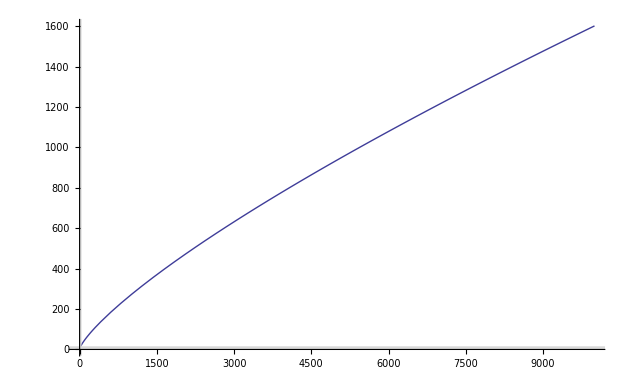

```mathematica
Plot[(2^((1/Log[11]+Log[63]/(Log[3] Log[7])) Log[1+x]) 3^((Log[55] Log[1+x])/(Log[5] Log[11])) Log[3] Log[5] Log[7] Log[11] (-Log[3] Log[5] Log[7] Log[11]+x (Log[2] Log[5] Log[7] Log[33]+Log[3] (Log[3] Log[7] Log[55]-Log[5] Log[11] Log[343/4]))))/((1+x)^3 (Log[3] Log[4] Log[5] Log[11]+Log[5] Log[7] (-Log[9] Log[11]+Log[2] Log[33])+Log[3]^2 Log[7] Log[55]) (Log[2] Log[5] Log[7] Log[33]+Log[3] (Log[3] Log[7] Log[55]-Log[5] Log[11] Log[343/4]))), {x,0,10000}, GridLines->{Range[25],Range[0,13]}]
```

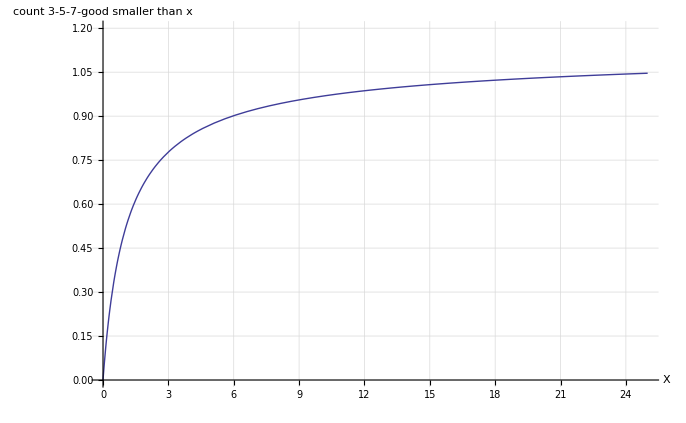

```mathematica
Plot[x chancep[3,x]chancep[5,x] chancep[7,x], {x,0,25}, PlotRange->{Automatic, {0,1.2}}, GridLines->Automatic, AxesLabel->{"X","count 3-5-7-good\nsmaller than x"},LabelStyle->{FontFamily->"Calibri", FontSize->Larger}]
```

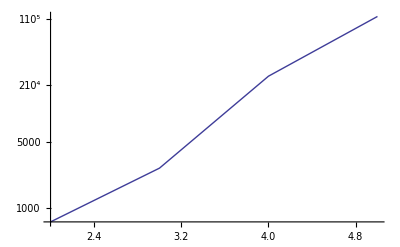

```mathematica
ListLogPlot[{0,714,2639,24664,105344}, Joined->True]
```

```mathematica
FindSequenceFunction[{0,714,2639,24664,105344}]
```

```mathematica
FindSequenceFunction[{0,714,2639,24664,105344},n]
```

```mathematica
InterpolatingPolynomial[{{0,0},{10^10,714},{10^20,2639},{10^30,24664},{10^50,105344}},n]
```

774739583410807291599294704863268229168600477431467274305407761501700717447919903949652981239149398327690988839605038051818576175455729154355598950003307290842031249901043749995885000002469/1808449074074074074055989583331524884259078414351869936342594401041666847511574074074074072265625000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

```mathematica
N[(714+(1211/2+(18889/6+9833/12 (-4+n)) (-3+n)) (-2+n)) (-1+n), n==1]
```

N::precbd: Requested precision n == 1 is not a machine-sized real number between $MinPrecision and $MaxPrecision.

```mathematica
n=6;(714+(1211/2+(18889/6+9833/12 (-4+n)) (-3+n)) (-2+n)) (-1+n)
```

302900

```mathematica
N[774739583410807291599294704863268229168600477431467274305407761501700717447919903949652981239149398327690988839605038051818576175455729154355598950003307290842031249901043749995885000002469/1808449074074074074055989583331524884259078414351869936342594401041666847511574074074074072265625000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000*10^60]
```

4.284×10^53